# Assignment 1

Load the files that contain randomized points x,y for each of the functions.

```mathematica
SetDirectory["C:\\Users\\brook\\Documents\\Workspaces\\CSC 450\\csc450"]
```

C:\Users\brook\Documents\Workspaces\CSC 450\csc450

```mathematica
FileNames[]
```

{bin,lib,points1.txt,points2.txt,points3.txt,points4.txt,points5.txt,src,.vscode}

## Comparing Functions

## Simple Polynomial

Load the randomized points for  the first function and plot them.

```mathematica
plotPts1=Import["points1.txt","CSV"];
sortedPlotPts1=Sort[plotPts1];
```

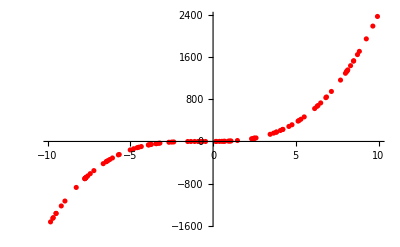

```mathematica
samplePts1=ListPlot[sortedPlotPts1,PlotStyle->{Red}]
```

```mathematica
f[x_]=2.0*x^3+4.0*x^2+2.0*x
```

2. x+4. x^2+2. x^3

Find the min and max of the data points from the sample data.

```mathematica
xMin1=First[sortedPlotPts1][[1]]
xMax1=Last[sortedPlotPts1][[1]]
```

-9.82259

9.93626

Plot the true plot of the same function.

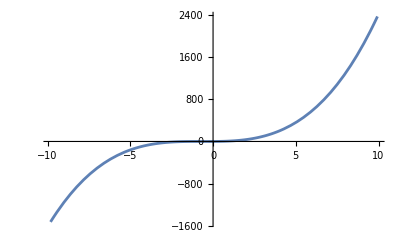

```mathematica
plot1=Plot[f[x],{x,xMin1,xMax1}]
```

Plot both the sample data (in red) and the true function (in blue). We see that the data points align on the curve.

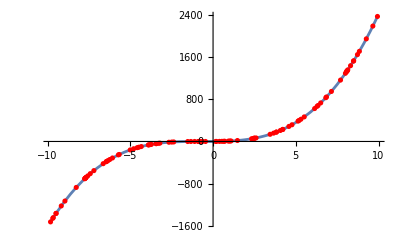

```mathematica
Show[{plot1,samplePts1}]
```

We can see that the points align right on the curve, which indicates no error yet.

```mathematica
plot1Trimmed = Plot[f[x],{x,4,8}];
```

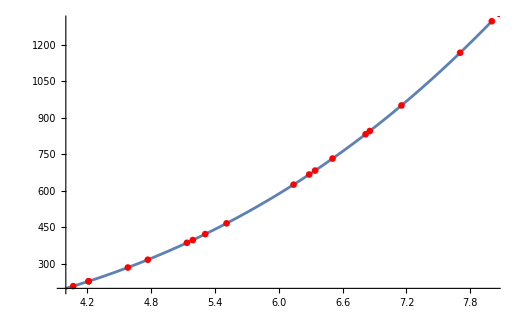

```mathematica
Show[{plot1Trimmed,samplePts1}]
```

## Simple Sin Function

Do another example of the same process with a sin function in order to test that other functions at this scale also do not have any error.
WIth this function we’ll be able to test small values produced such as sin(Pi) which would be very, very close to 0 but not quite.

In this case, I got about 3, which was to be expected. g(Pi) = 2.9999995

```mathematica
plotPts2=Import["points2.txt","CSV"];
sortedPlotPts2=Sort[plotPts2];
```

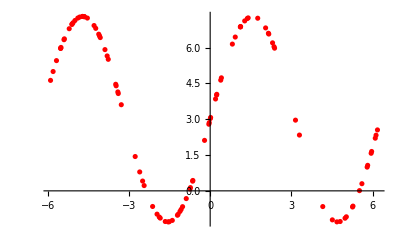

```mathematica
samplePts2=ListPlot[sortedPlotPts2,PlotStyle->{Red}]
```

Repeating the same process as the previous example.

```mathematica
g[x_]=4.3*Sin[x]+3.0
```

3.+4.3 Sin[x]

```mathematica
xMin2=First[sortedPlotPts2][[1]]
xMax2=Last[sortedPlotPts2][[1]]
```

-5.89579

6.17854

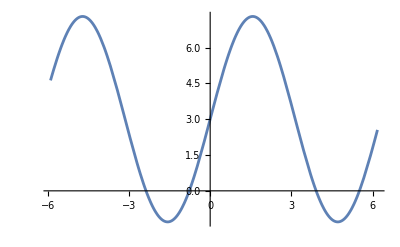

```mathematica
plot2=Plot[g[x],{x,xMin2,xMax2}]
```

We can see that the data overlaps nicely again.

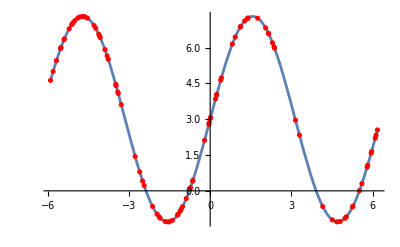

```mathematica
Show[{plot2,samplePts2}]
```

Taking a smaller range also

```mathematica
plot2Trimmed = Plot[g[x],{x,-2,-1}];
```

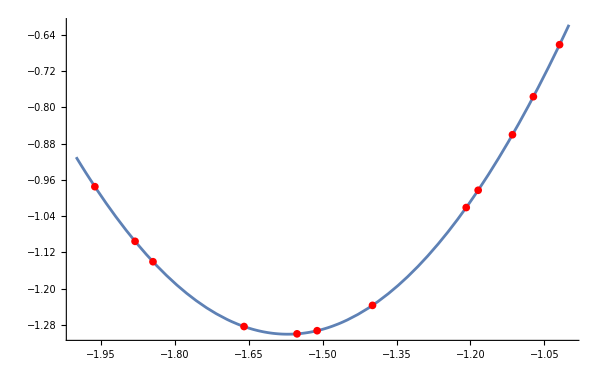

```mathematica
Show[{plot2Trimmed,samplePts2}]
```

## Composition of Functions

For the last function, I decided to create a composition of 1D Functions class that would take two Function1D objects to create F(G(x)).

This would allow me to create much more interesting functions to examine the behavior of in addition to the sin and cos functions.

```mathematica
plotPts3=Import["points3.txt","CSV"];
sortedPlotPts3=Sort[plotPts3];
```

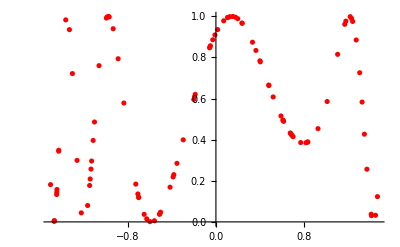

```mathematica
samplePts3=ListPlot[sortedPlotPts3,PlotStyle->{Red}]
```

```mathematica
h[x_] =(Sin[(x^4+-2.0*x+5.0)])^2
```

Sin[5.-2. x+x^4]^2

```mathematica
xMin3=First[sortedPlotPts3][[1]]
xMax3=Last[sortedPlotPts3][[1]]
```

-1.49637

1.4617

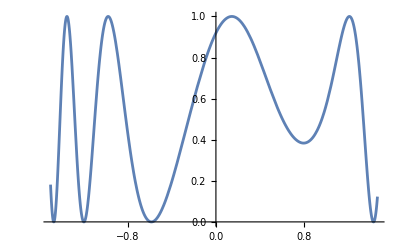

```mathematica
plot3=Plot[h[x],{x,xMin3,xMax3}]
```

We can see even with complex functions such as this one, there still isn’t any apparent error.

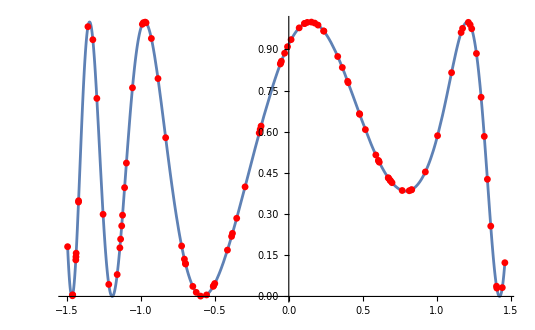

```mathematica
Show[{plot3,samplePts3}]
```

A few areas of interest at different scales...

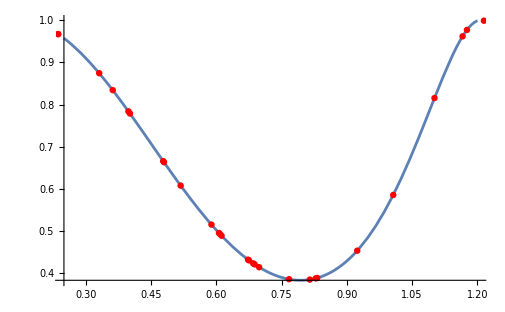

```mathematica
plot3Trimmed = Plot[h[x],{x,0.25,1.2}];
Show[{plot3Trimmed,samplePts3}]
```

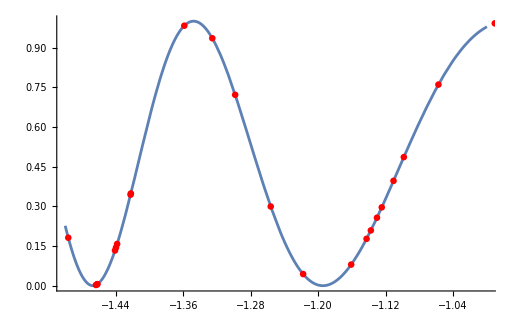

```mathematica
plot3Trimmed2 = Plot[h[x],{x,-1.5,-1.0}];
Show[{plot3Trimmed2,samplePts3}]
```

## Functions with Error

## Function #1

So far we’ve seen functions with very minimal error due to the easy numbers. 

Regarding this simple function, the operations of squaring X, adding one, and then taking the square root and subtracting one can showcase minor error produced during operations as well as on tiny numbers.

```mathematica
plotPts4=Import["points4.txt","CSV"];
sortedPlotPts4=Sort[plotPts4];
```

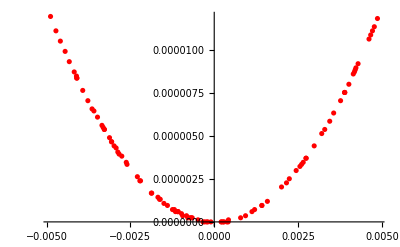

```mathematica
samplePts4=ListPlot[sortedPlotPts4,PlotStyle->{Red}]
```

```mathematica
k[x_] = ((x^2)+1.0)^(1/2.0)+-1.0
```

-1.+(1.+x^2)^0.5

```mathematica
xMin4=First[sortedPlotPts4][[1]]
xMax4=Last[sortedPlotPts4][[1]]
```

-0.00488059

0.00486722

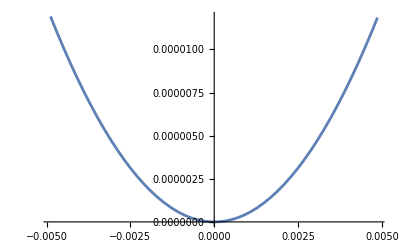

```mathematica
plot4=Plot[k[x],{x,xMin4,xMax4}]
```

From a distance, we can see that the function is pretty much the same, but viewing certain sections of the function shows a bit of variability in the data points vs. the true graph.

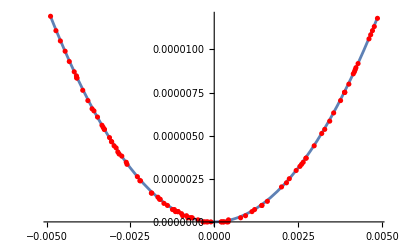

```mathematica
Show[{plot4,samplePts4}]
```

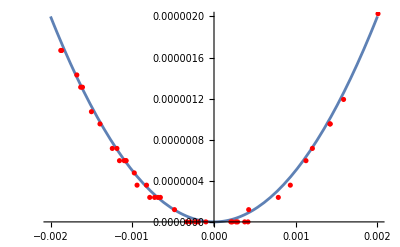

```mathematica
plot4Trimmed = Plot[k[x],{x,-0.002,0.002}];
Show[{plot4Trimmed,samplePts4}]
```

And zooming in even further shows more variability. With very small numbers, as there is right now, can cause floating point errors.

The smaller the values get, the more apparent error there is.

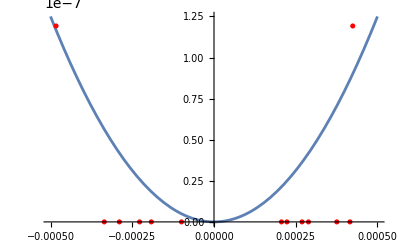

```mathematica
plot4Trimmed = Plot[k[x],{x,-0.0005,0.0005}];
Show[{plot4Trimmed,samplePts4}]
```

## Function #2

Similarly, how about error with very large numbers? 

Repeating the same process of potting randomized points against the true plot gives us...

```mathematica
plotPts5=Import["points5.txt","CSV"];
sortedPlotPts5=Sort[plotPts5];
```

```mathematica
samplePts5=ListPlot[sortedPlotPts5,PlotStyle->{Red}]
```

-Graphics-

```mathematica
n[x_]=x^5+10^8 x^4+10^7 x^3+10^6 x^2+10^5 x+10^4
```

10000+100000 x+1000000 x^2+10000000 x^3+100000000 x^4+x^5

```mathematica
xMin5=First[sortedPlotPts5][[1]]
xMax5=Last[sortedPlotPts5][[1]]
```

129621.

963857.

```mathematica
plot5=Plot[n[x],{x,xMin5,xMax5}]
```

-Graphics-

We can see that graphing the pure function against the computed random values produce a surprisingly sound graph.

```mathematica
Show[{plot5,samplePts5}]
```

-Graphics-

```mathematica
n2[x_]=x^5+10^8 x^4+10^7 x^3+10^6 x^2+10^5 x+10^4
```

10000+100000 x+1000000 x^2+10000000 x^3+100000000 x^4+x^5

Even wen viewing closer, the points still align on the curve. However, let’s instead of graphing n[x] using the pure original function I was intending, let’s graphing the function after the coefficients were already computed and NOT computed in Mathematica.

```mathematica
plot5Trimmed = Plot[n[x],{x,700000,800000}];
Show[{plot5Trimmed,samplePts5}]
```

-Graphics-

What I mean is given a function p[x] with the computed coefficients with the floating point calculations in the library. The coefficients are slightly different. Graphing these functions together shows the error.

```mathematica
n[x_]=x^5+10^8 x^4+10^7 x^3+10^6 x^2+10^5 x+10^4
```

10000+100000 x+1000000 x^2+10000000 x^3+100000000 x^4+x^5

```mathematica
p[x_] =x^5+1.0E+8*x^4+1.0E+7*x^3+1000000.0*x^2+100000.0*x+10000.0
```

10005.4+100000. x+1.×10^6 x^2+7 x^3+8 x^4+x^5

The plot of p[x] from a distance looks the same as n[x].

```mathematica
plot6=Plot[p[x],{x,xMin5,xMax5}]
```

-Graphics-

When graphing the randomized points from function and seeing the calculated version of the function n[x], we can see the striking difference between the two curves.

Based on the slight changes to the coefficients for p[x], at such large numbers as we are now, even minor alterations can have large impacts in the function, and the impact only grows and grows.

```mathematica
Show[{plot6,samplePts5}]
```

-Graphics-